```mathematica
(*Example 10 map from Article, see article_example10.m (Matlab) for numerical calculation*)
A1={{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}};
A2={{0,0,1,0},{0,2,0,1},{1,0,2,0},{0,1,0,0}};
A3={{0,0,0,1},{0,-1,1,0},{0,1,1,0},{1,0,0,0}};
A4=IdentityMatrix[4];
A={A1,A2,A3,A4};
A1//MatrixForm
A2//MatrixForm
A3//MatrixForm
A4//MatrixForm
(* defining y=f(x) *)
y1={x1, x2, x3,x4}.A1.{x1,x2,x3,x4};
y2={x1, x2, x3,x4}.A2.{x1,x2,x3,x4};
y3={x1, x2, x3,x4}.A3.{x1,x2,x3,x4};
y4={x1, x2, x3,x4}.A4.{x1,x2,x3,x4};
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(0 | 0 | 1 | 0
0 | 2 | 0 | 1
1 | 0 | 2 | 0
0 | 1 | 0 | 0)

(0 | 0 | 0 | 1
0 | -1 | 1 | 0
0 | 1 | 1 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Taking the solution x(Y), replacing root with List, taking the polynomial out. |x|=1 equivalent to y4=1, y3=0 -- required section *)
S = Solve[y1==Y1 && y2 ==Y2 && y3 ==0&&y4==1 , {x1, x2, x3,x4}] 
(*Poly:=((List @@ (x1/.S[[1]]))[[1]])*)
```

{{x1→(2891+1-17633828628725760 Y2^17 Root[1&,1]^(15/2))/(-21771583488 Y1^5+90311491584 Y1^6+543702122496 Y1^7-2146113552384 Y1^8-6230082191360 Y1^9+21101197819904 Y1^10+448+4121940261696 Y1 Y2^22+3199036688816 Y1^2 Y2^22-182521675136 Y2^23-297981538240 Y1 Y2^23+12456203392 Y2^24),x2→-√Root[16 Y1^6-72 Y1^7+42+10616832 #1^8&,1],x3→1/1,x4→(2887+1)/(463+1-12456203392 Y2^24)},{1},12,{1},{1}}
 |  |  |  |

```mathematica
Poly:=((List @@ (x1/.S[[1]]))[[1]])
```

```mathematica
(* Care about the boundary -> taking discriminant *)
(*Quq=Discriminant[Poly[z], z]*)
x1/.S[[1]]
```

1/(-21771583488 Y1^5+90311491584 Y1^6+543702122496 Y1^7-2146113552384 Y1^8-6230082191360 Y1^9+21101197819904 Y1^10+43118803828736 Y1^11-108855899410432 Y1^12-191549048087552 Y1^13+298860497344768 Y1^14+431+274515167440288 Y1^3 Y2^20+99443301567828 Y1^4 Y2^20-3924209677184 Y2^21-24849559474176 Y1 Y2^21-42663502339168 Y1^2 Y2^21-21174859225568 Y1^3 Y2^21+1141798429568 Y2^22+4121940261696 Y1 Y2^22+3199036688816 Y1^2 Y2^22-182521675136 Y2^23-297981538240 Y1 Y2^23+12456203392 Y2^24)
 |  |  |  |

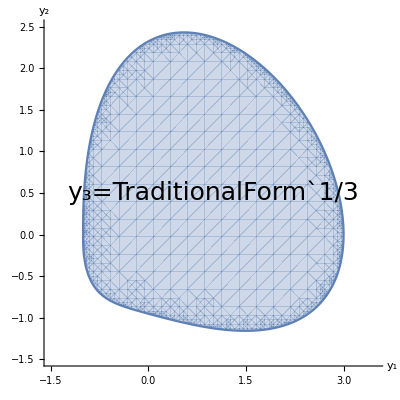

```mathematica
(* Plotting first section y3=1/3. We are lucky and can just take poly2 ≤ 0 *)
Y3sec =1/3;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
RegionPlot[poly2≤0,{Y1,-1.5,3.5},{Y2,-1.5,2.5},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

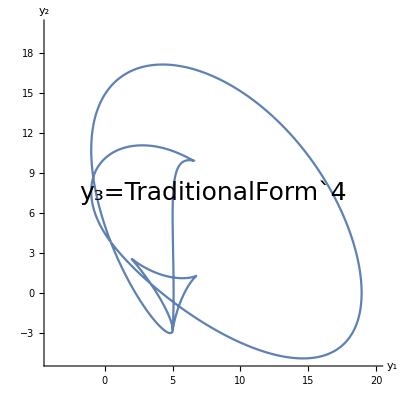

```mathematica
(* Plotting the y3=4 section. Less lucky, RegionPlot doesn't work, so we use polar plot manually (furthest point) *)
Y3sec =4;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
plot=ContourPlot[poly2==0,{Y1,-4,20},{Y2,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
(* points from the plot *)
points=Cases[Normal@plot,Line[pts_,___]:>pts,Infinity];
list=Flatten[points,1];
```

```mathematica
(* shifting the points so that polar coordinates from the point inside map it properly (assessed visually) *)
xdiff=4;
ydiff=0;
pts=list+ConstantArray[{-xdiff,-ydiff},Length[list]];
```

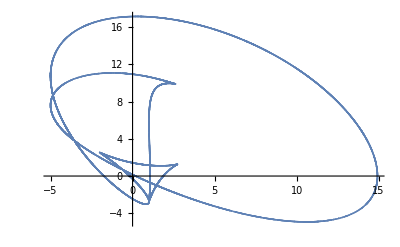

```mathematica
ListPlot[pts]
```

```mathematica
(* going to polar coordinates *)
r=Norm/@pts;
phi=(ArcTan@@#1)&/@pts;
d=0.01; (* threshold angle *)
(* function: max r s.t. exist a point on a ray alpha in pts *)
rad[alpha_]:=Max[MapThread[If[#1≤d,r[[#2]],0]&,{Abs[phi-alpha],Range[1,Length[phi]]}]];
```

```mathematica
(* ranges of phis, and corresponding Rs *)
phis1=Range[-Pi,Pi,0.01];
rs1=rad/@phis1;
```

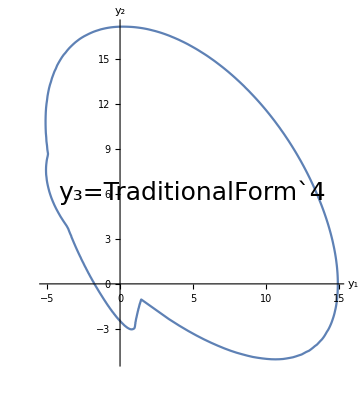

```mathematica
(* plotting in polar coordinates *)
ListPolarPlot[Transpose[{phis1,rs1}],Joined->True,Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

Nearest::dmtch: The dimension of {-3.14159, -3.13159, -3.12159, -3.11159, -3.10159, -3.09159, -3.08159, -3.07159, -3.06159, -3.05159, -3.04159, -3.03159, « 28 », -2.74159, -2.73159, -2.72159, -2.71159, -2.70159, -2.69159, -2.68159, -2.67159, -2.66159, -2.65159, « 579 »} and ArcTan[-4 + x, y] does not match.

Part::pkspec1: The expression ArcTan[-4 + x, y] cannot be used as a part specification.

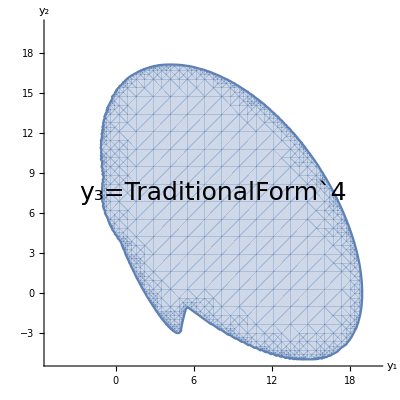

```mathematica
(* plotting the area inside *)
(* closest phi angle *)
nf=Nearest[phis1->Automatic];
(* is this point inside the shape? *)
IsInside[x_,y_]:=Norm[{x-xdiff,y-ydiff}]≤rs1[[nf[ArcTan[x-xdiff,y-ydiff]][[1]]]];
(* plotting the shape *)
RegionPlot[IsInside[x,y],{x,-5,20},{y,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```